```mathematica
k=3/4;
s=50;
r=.55;
b0=.01;
```

```mathematica
NSolve[x^((k-1)/(2-k))*(x*μ*(s-1)-r)==(μ*(s-1)/(b0^.25*r^(-.25)))^(1/(2-k))/.{μ-> 10^(-2)r*b0^.25/s},x]
```

{{x→348.395}}

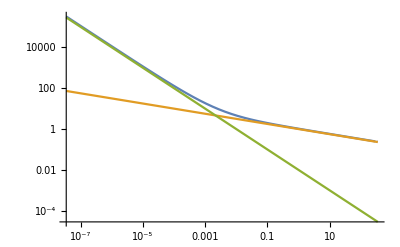

```mathematica
LogLogPlot[{x/.NSolve[x^((k-1)/(2-k))*(x*μ*(s-1)-r)==(μ*(s-1)/(b0^.25*r^(-.25)))^(1/(2-k)),x],μ^(-.25),0.01*μ^(-1)},{μ,10^(-5)*r*b0^.25/s,10^(5)*r*b0^.25/s},PlotRange->All]
```